```mathematica
Clear["Global`*"]
```

```mathematica
options=<|{1->"a63a108c",2->"clarky",3->"e205",4->"e374",5->"l7769",6->"naca747a315",7->"naca4412",8->"naca23012",9->"naca642415",10->"s1223",11->"sd7003",12->"usa35b"}|>;

(* change the index in the options association to change the airfoil *)
air=options[4];
Print[Style["The chosen airfoil is the airfoil ",FontFamily->"Oswald",Italic,Black,20],Style[StringTemplate["`a`"][<|"a"->air|>],FontFamily->"Oswald",Italic,Red,30]]
```

The chosen airfoil is the airfoil e374

```mathematica
(* Import Paclets *)
Needs["NDSolve`FEM`"]
Needs["FEMAddOns`"]
```

```mathematica
list=Import[StringTemplate["/Users/gustavomanzari/GitHub/Numerical-Simulation-for-NACA-Airfoil-with-Spalart-Allmaras-Turbulence-Model/Airfoil Data/`l`.dat"][<|"l"->air|>]];
pos={};
neg={};
app=DeleteCases[DeleteDuplicates[Sort[list[[2;;-1]]]],{}];
Do[If[app[[i,2]]<0,AppendTo[neg,app[[i]]],AppendTo[pos,app[[i]]]],{i,1,Dimensions[app][[1]]}];
coords=Join[pos,Reverse[neg],{pos[[1]]}];
{ymin,ymax}=MinMax[coords[[1;;-1,2]]];
Animate[seg={};
Do[AppendTo[seg,{coords[[i]],coords[[i+1]]}],{i,1,j}];
ListLinePlot[Flatten[seg,1],PlotRange->{{-0.05,1.05},{2ymin,2ymax}},AspectRatio->Automatic,PlotStyle->Red],
{j,1,Dimensions[coords][[1]]-1},AnimationRunning->True]
```

Part::partw: Part 2 of {E374} does not exist.

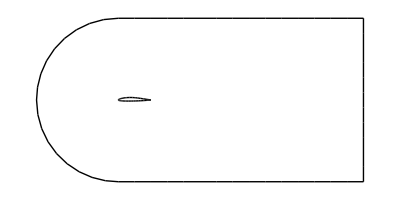

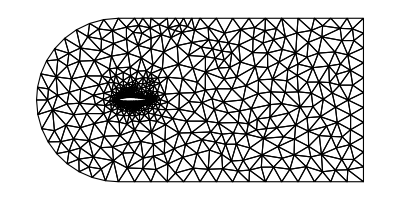

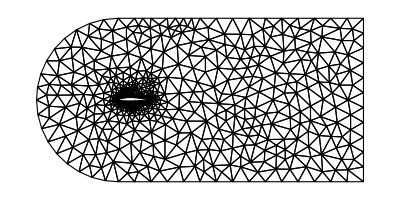

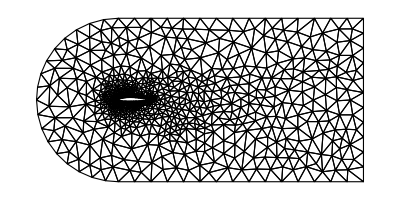

```mathematica
(* Mesh-Generation *)
(* choose the airfoil .dat file *)
airfoilDATA=Import[StringTemplate["`dir`Airfoil Data/`airfoil`.dat"][<|"dir"->ToString[NotebookDirectory[]],"airfoil"->air|>]];
airfoilClass=StringTemplate["`a``b`"][<|"a"->airfoilDATA[[1,1]],"b"->airfoilDATA[[1,2]]|>];
dataArray={a,b};
dataArray[[1]]=airfoilDATA[[2;;-1]];
dataArray[[2]]=Polygon[dataArray[[1]]];
(* choose domain-size (1-length = 1-cord-length) *)
H=5; (* Domain height in cord-lengths *)
L=2*H;(* Domain Depth in cord-lengths *)
ℓ=H/5; (* Refining region core dimension in cord-lengths *)
B=(2H)/4;
Clear[x,𝓍];
𝓍rule=Solve[ℓ/(L-H/2+𝓍)==B/𝓍,𝓍];
𝓍=Abs[𝓍/.𝓍rule[[1]]];
region=ImplicitRegion[{(x^2+y^2≤(H/2)^2&& x≤0)||(x≥0&&y≤H/2&&y≥-H/2&&x≤L-H/2)},{x,y}];
Ω=RegionUnion[Disk[{0,0},H/2],Rectangle[{0,-H/2},{L-H/2,H/2}]];
bmesh1=ToBoundaryMesh[Ω];
bmesh2=ToBoundaryMesh[dataArray[[2]]];
ΩBoundaries=BoundaryElementMeshDifference[bmesh1,bmesh2];
ΩBoundaries["Wireframe"]
(* choose mesh-refining function *)
meshrefine[vertices_,area_]:=area>1/H;
f=Function[{vertices,area},area>1/(5 H^2) (10 Norm[Mean[vertices]])];
pred=(x^2+y^2≤(ℓ/2)^2||x≥0&&-((ℓ-B)/(H-2L))x-y≤ℓ/2&&((ℓ-B)/(H-2L))x-y≥-ℓ/2&&x≤L-H/2);
g=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[pred,area>1/(5 H^3) (0.01+10 Norm[Mean[vertices]]),area>1/(5 H^2) (0.01+10 Norm[Mean[vertices]])]]];
mesh1=ToElementMesh[ΩBoundaries,MeshQualityGoal->"Maximal",MeshRefinementFunction->meshrefine];
mesh1["Wireframe"]
mesh2=ToElementMesh[ΩBoundaries,MeshQualityGoal->"Maximal",MeshRefinementFunction->f];
mesh2["Wireframe"]
mesh3=ToElementMesh[ΩBoundaries,MeshQualityGoal->"Maximal",MeshRefinementFunction->g];
mesh3["Wireframe"]
```

```mathematica
(* Snippet of data acquiring *)
```

```mathematica
Clear[coords,center,newcoords,combinations,vectors,sides,centermidvectors,ns]
```

```mathematica
(* Surface Vectors computing *)
Clear[coords]
(* input => cell coordinates *)
center=Mean[coords];
newcoords=Table[coords[[i]]-center,{i,1,3}];
combinations=Subsets[newcoords,{2}];
vectors=Table[combinations[[i,1]]-combinations[[i,2]],{i,1,3}];
sides=Subsets[newcoords,{2}];
centermidvectors=Table[Mean[sides[[i]]]-Mean[newcoords],{i,1,3}];
ns=Table[N[Norm[sides[[i]]]*(Mean[sides[[i]]]-Projection[centermidvectors[[i]],vectors[[i]]])/Norm[Mean[sides[[i]]]-Projection[centermidvectors[[i]],vectors[[i]]]]],{i,1,3}];
{xmin,xmax}={Min[Transpose[newcoords][[1]]],Max[Transpose[newcoords][[1]]]};
{ymin,ymax}={Min[Transpose[newcoords][[2]]],Max[Transpose[newcoords][[2]]]};
m=0.9;
Show[ListPlot[{Mean[newcoords]},PlotStyle->Red,PlotRange->{{xmin-m(xmax-xmin),xmax+m(xmax-xmin)},{ymin-m(ymax-ymin),ymax+m(ymax-ymin)}}],Graphics[{Green,Opacity[0.5],Triangle[newcoords]}],Graphics[{Red,Arrow[{Mean[newcoords],Mean[{newcoords[[1]],newcoords[[2]]}]}],Arrow[{Mean[newcoords],Mean[{newcoords[[1]],newcoords[[3]]}]}],Arrow[{Mean[newcoords],Mean[{newcoords[[2]],newcoords[[3]]}]}]}],Graphics[{Arrow[{Mean[sides[[1]]],Mean[sides[[1]]]+ns[[1]]}],Arrow[{Mean[sides[[2]]],Mean[sides[[2]]]+ns[[2]]}],Arrow[{Mean[sides[[3]]],Mean[sides[[3]]]+ns[[3]]}]}]]
```

```mathematica
M∞=;
α=;
u∞=M∞*Cos[α];
v∞=M∞*Sin[α];
ρ∞=1;
a∞=1;
p∞=1/γ;
```

```mathematica
uv={u[t,x,y],v[t,x,y]}; pxy=p[t,x,y]; ℰ=En[t,x,y];ρxy=ρ[t,x,z]; τxx=(μ+μt)((μ∞)/(ρ∞ c a∞))(-2/3 Derivative[0,0,1][v][t,x,y]+4/3 Derivative[0,1,0][u][t,x,y]);
τyy=(μ+μt)((μ∞)/(ρ∞ c a∞))(4/3 Derivative[0,0,1][v][t,x,y]-2/3 Derivative[0,1,0][u][t,x,y]);
τxy=(μ+μt)((μ∞)/(ρ∞ c a∞))(Derivative[0,0,1][u][t,x,y]+Derivative[0,1,0][v][t,x,y]);
```

```mathematica
U={ρxy,ρxy uv[[1]],ρxy uv[[2]], ℰ};
F={ρxy uv[[1]],ρxy uv[[1]]^2+ρxy,ρxy uv[[1]] uv[[2]],uv[[1]](ℰ+pxy)};
G={ρxy uv[[2]],ρxy uv[[1]] uv[[2]],ρxy uv[[2]]^2+ρxy,uv[[2]](ℰ+pxy)};
Fv={0,τxx,τxy,τxx uv[[1]]+τxy uv[[2]]};
Gv={0,τxy,τyy,τxy uv[[1]]+τyy uv[[2]]};
S={0,0,0,0};
NS=Table[D[U[[i]],t]+D[F[[i]],x]+D[G[[i]],y]-D[Fv[[i]],x]-D[Gv[[i]],y],{i,1,4}];
MatrixForm[NS]
```

```mathematica
bc= {DirichletCondition[uv[[1]]==u∞,x^2+y^2==(H/2)^2&&x≤0],
DirichletCondition[uv[[2]]==v∞,x^2+y^2==(H/2)^2&&x≤0],
DirichletCondition[ρxy==ρ∞,x^2+y^2==(H/2)^2&&x≤0],
DirichletCondition[a[x,y]==a∞,x^2+y^2==(H/2)^2&&x≤0],
DirichletCondition[pxy==p∞,x^2+y^2==(H/2)^2&&x≤0],
DirichletCondition[ℰ==(p∞)/(γ-1)+(ρ∞)/2((u∞)^2+(v∞)^2),x^2+y^2==(H/2)^2&&x≤0],
DirichletCondition[{u[x,y]==4*0.3*y*(h-y)/h^2,v[x,y]==0},x==0],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},y==0||y==h||(x-1/5)^2+(y-1/5)^2<=(1/20)^2]};
```